# Compound Matrix Method

#### Implementation using the Compound Matrix Method to calculate the Evans function, in order to solve boundary value eigenvalue problems.

## Installation

The following command will install the most recent version from the PacletServer:

```mathematica
Needs["PacletManager`"]
PacletInstall["CompoundMatrixMethod","Site"->"http://raw.githubusercontent.com/paclets/PacletServer/master"]
```

Paclet[CompoundMatrixMethod,0.8,<>]

We need to load the package:

```mathematica
Needs["CompoundMatrixMethod`"]
```

```mathematica
PacletUninstall["CompoundMatrixMethod"]
SetDirectory[NotebookDirectory[]]
pac=PackPaclet["CompoundMatrixMethod"];
PacletInstall[pac]
Needs["CompoundMatrixMethod`"]
```

/Users/spearce/Dropbox (The University of Manchester)/Mathematica/Packages

Paclet[CompoundMatrixMethod,0.9,<>]

## Examples

Example 1: Second order equation with constant coefficients

Second order ODE: y''(x) + λ^2 y(x) =0, subject to y(0)=y(L)=0. The roots to this can be found analytically to be nπ/L, n ∈ ℤ. 
Converting to a matrix equation, we let y_1=y,y_2=y', then y_1'=y_2,y_2'=-λ^2 y_1 and hence y' =A y, where A=(0 | 1
-λ^2 | 0).
These boundary conditions can be written as matrices as B=C=(1 | 0
0 | 0).

We can then evaluate the Evans function at a given value of λ=λ_0, e.g. for λ=1  (with L=2):

```mathematica
Evans[{λ,1},({{0, 1}, {-λ^2, 0}}),({{1, 0}, {0, 0}}),({{1, 0}, {0, 0}}),{x,0,2}]
```

0.909297

This function is analytic, and its zeroes correspond to eigenvalues of the original system:

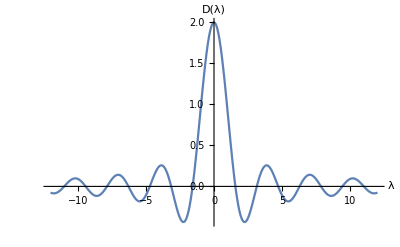

```mathematica
With[{L=2},
Plot[Evans[{λ,λ0},({{0, 1}, {-λ^2, 0}}),({{1, 0}, {0, 0}}),({{1, 0}, {0, 0}}),{x,0,2}],{λ0,-12,12},AxesLabel->{"λ","D(λ)"},PlotRange->All]]
```

FindRoot will converge to a root:

```mathematica
With[{L=2},FindRoot[Evans[{λ,λ0},({{0, 1}, {-λ^2, 0}}),({{1, 0}, {0, 0}}),({{1, 0}, {0, 0}}),{x,0,2}],{λ0,20}]]
```

{λ0→20.4204}

However, the easier way to feed the system to Evans is to use the function ToMatrixSystem:

```mathematica
sys=ToMatrixSystem[y''[x]+λ^2 y[x]==0,{y[0]==0,y[L]==0},y,{x,0,L},λ];
```

This returns all the components needed to generate the Evans function at a given λ. Note that the Evans function now does not require specifying which variable is the eigenvalue, as it has been specified already.

```mathematica
Evans[1,sys/.L->1]
```

0.841471

And gives the same plot as before:

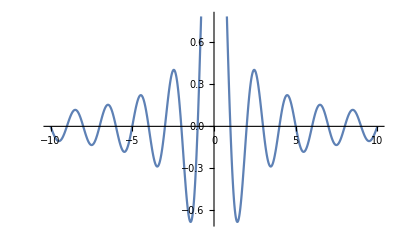

```mathematica
Plot[Evans[λ,sys/.L->π],{λ,-10,10}]
```

```mathematica
FindRoot[Evans[λ,sys/.L->π],{λ,0.1}]
```

{λ→3.}

We could also change the boundary values, e.g. for y(0)+2 y'(0)=0, y'(L)=0.

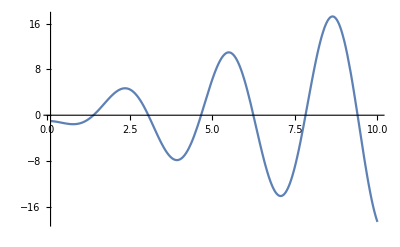

```mathematica
sys1b=ToMatrixSystem[y''[x]+λ^2 y[x]==0,{y[0]+2y'[0]==0,y'[L]==0},y,{x,0,L},λ];
Block[{L=2},Plot[Evans[λ0,sys1b],{λ0,0.1,10}]]
```

Example 2: Second order equation with complex constant coefficients

This method also works for complex equations , here is y’(x) = ⅈ y(x) + z(x), z'(x)=-λ^2 y(x) + (1-ⅈ)z(x)

```mathematica
sys2=ToMatrixSystem[{y'[x]==I y[x] +z[x],z'[x]==-λ^2 y[x]+(1-I)z[x]},{y[0]==0,y[2]==0},{y,z},{x,0,2},λ]
```

{{{ⅈ,1},{-λ^2,1-ⅈ}},{{1,0}},{{1,0}},{x,0,2}}

Can find complex roots using FindRoot:

```mathematica
FindRoot[Evans[λ,sys2],{λ,5}]
```

{λ→4.63339-0.107912 ⅈ}

We can plot the real and imaginary parts in the complex plane, where intersections of the two curves show roots.

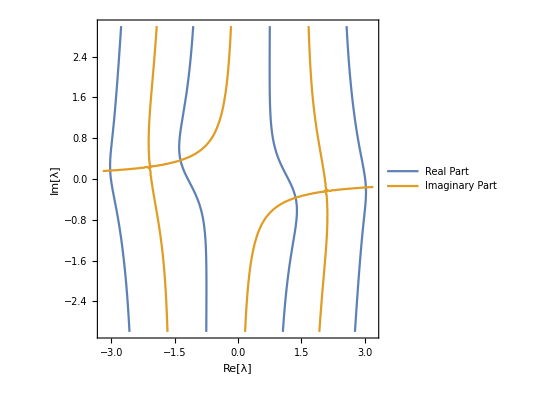

```mathematica
ContourPlot[{Re[Evans[λr+I λi,sys2]]==0,Im[Evans[λr+I λi,sys2]]==0},{λr,-3.2,3.2},{λi,-3,3},PlotPoints->30,FrameLabel->{"Re[λ]","Im[λ]"},PlotLegends->{"Real Part","Imaginary Part"}]
```

Example 3: Third order equation with complex eigenvalues (and winding number tutorial)

The method also works for odd order equations, for instance y'''- λ^3 y=0, y(0)=y'(0)=0, y(π)=0. 
This equation can be solved directly using DSolve, and has a range of complex roots

```mathematica
yex3=DSolve[{y'''[x]-λ^3 y[x]==0},y,{x,0,π}][[1]];
cofmat=Table[Coefficient[{y[0]==0,y'[0]==0,y[π]==0}/.yex3/.Equal->Subtract,C[i]],{i,1,3}];
ex3detsol=Solve[{Simplify[Det[cofmat]]==0,-5≤Re@λ≤15,-15≤Im@λ≤15}]//Chop;
```

ToMatrixSystem gives the 3x3 matrix A, and assigns the boundary conditions correctly.

```mathematica
sys3=ToMatrixSystem[y'''[x]-λ^3 y[x]==0,{y[0]==0,y'[0]==0,y[π]==0},y,{x,0,π},λ]
```

{{{0,1,0},{0,0,1},{λ^3,0,0}},{{1,0,0},{0,1,0}},{{1,0,0}},{x,0,π}}

```mathematica
FindRoot[Evans[λ,sys3],{λ,1+I}]
```

{λ→0.673736+1.16694 ⅈ}

Again, we can use ContourPlot to see graphically the solutions (increase PlotPoints to improve the accuracy, at a cost of computational time):

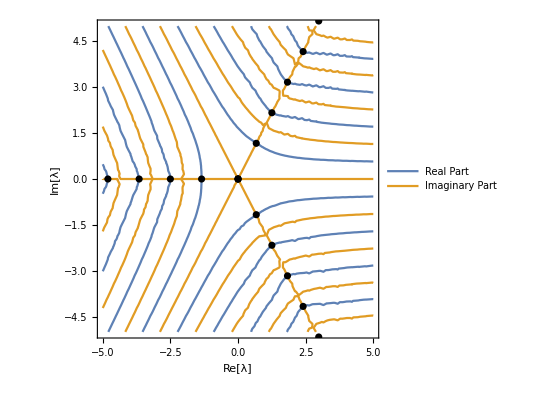

```mathematica
conplot=Show[{ContourPlot[{Re[Evans[λr+I λi,sys3]]==0,Im[Evans[λr+I λi,sys3]]==0},{λr,-5,5},{λi,-5,5},PlotPoints->20,FrameLabel->{"Re[λ]","Im[λ]"},PlotLegends->{"Real Part","Imaginary Part"}],ListPlot[ReIm[λ/.ex3detsol],PlotStyle->Black]}]
```

We can use the winding number to find how many roots are inside a contour (as the Evans function is analytic). 
This is implemented for both circular and semicircular contours (incorporating the positive half-plane).

Here plot the system with a contour of radius 1 (the contour discretization is automatically set to be r/50), which does not include a root.
We can see that the contour does not go round the origin in the D(λ) plane. Note that the contour overlaps itself here (which is why the lines look jagged).

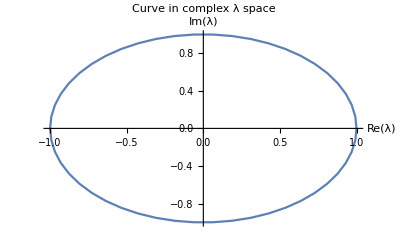

```mathematica
PlotEvansCircle[sys3,ContourRadius->1,Joined->True]
```

If we move the circle, the Evans function contour now goes round the origin, and hence the winding number is 1.

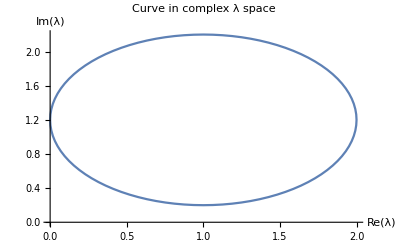

```mathematica
PlotEvansCircle[sys3,ContourCenter->1+1.2I,nPoints->100,Joined->True]
```

If we enlarge the circle at the origin, the contour now winds round the origin multiple times, and hence the Winding Number increases.

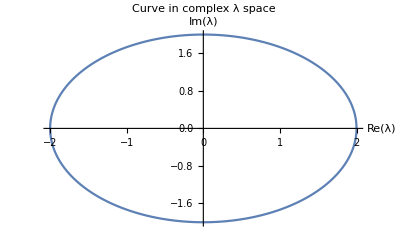

```mathematica
PlotEvansCircle[sys3,ContourRadius->2,Joined->True,nPoints->200]
```

We can see how the winding number increases as we traverse the contour:

```mathematica
inpts=CircleContour[2];
evanpts=Evans[#,sys3]&/@inpts;
Manipulate[GraphicsRow[{Show[ListPlot[ReIm@inpts[[1;;ii]],PlotRange->MinMax/@Transpose@ReIm@N@inpts],ListPlot[ReIm[λ/.ex3detsol],PlotStyle->Black],PlotLabel->"Contour in complex λ space",AxesLabel->{"Re(λ)","Im(λ)"}],ListPlot[ReIm@evanpts[[1;;ii]],Joined->True,PlotRange->MinMax/@Transpose@ReIm@evanpts,PlotLabel->"Evans function in complex space",AxesLabel->{"Re(D(λ))","Im(D(λ))"}]},ImageSize->900,PlotLabel->"Winding Number: "<>ToString@WindingNumber[ReIm@evanpts[[1;;ii]],{0,0}]],{{ii,3,"Angle"},3,Length[evanpts],1},SaveDefinitions->True]
```

A semicircular contour centred at the origin (and including the imaginary axis) can also be used:

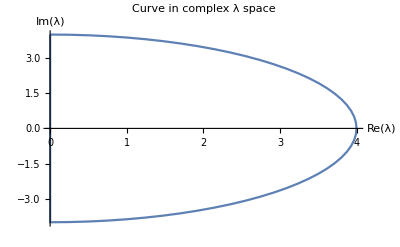

```mathematica
PlotEvansSemiCircle[sys3,ContourRadius-> 4,nPoints->100,Joined->True]
```

If the discretization of the contour is not sufficient, the winding number will not be accurate:

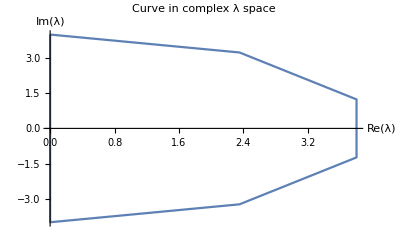

```mathematica
PlotEvansSemiCircle[sys3,ContourRadius-> 4,nPoints-> 10,Joined->True]
```

Note also that if the numbers from Evans overflow then the  winding number will also be incorrect

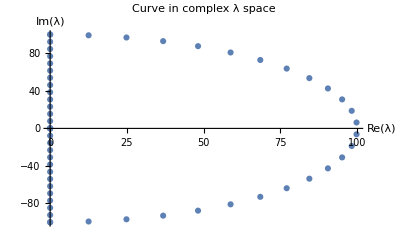

```mathematica
PlotEvansSemiCircle[sys3,ContourRadius-> 100,NormalizationConstants->0]
```

The winding number can be found explicitly via two functions:

```mathematica
WindingNumberCircle[sys3, ContourRadius->1]
WindingNumberSemiCircle[sys3,ContourRadius->3]
```

0

4

Example 4: Fourth order equation with non-constant coefficients

ϵ^4 y''''(x)+2 ϵ^2 λd/dx[sin(x)dy/dx]+y==0, subject to y (0)==y''(0)==y'(π/2)==y'''(π/2)==0.

Using the  function to put the system into the matrix form:

```mathematica
sys4=ToMatrixSystem[ϵ^4 y''''[x]+2 ϵ^2 λ D[Sin[x]y'[x],x]+y[x]==0,{y[0]==0,y''[0]==0,y'[π/2]==0,y'''[π/2]==0},y,{x,0,π/2},λ]
```

{{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-1/ϵ^4,-(2 λ Cos[x])/ϵ^2,-(2 λ Sin[x])/ϵ^2,0}},{{1,0,0,0},{0,0,1,0}},{{0,1,0,0},{0,0,0,1}},{x,0,π/2}}

Plotting the function shows several roots:

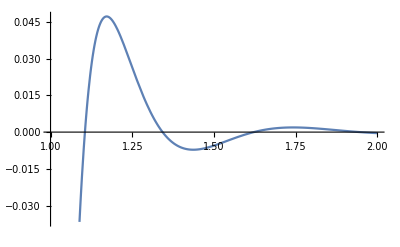

```mathematica
Plot[Evans[λ,sys4/.ϵ->0.1],{λ,1,2}]
```

FindRoot will converge to different roots for different starting points:

```mathematica
FindRoot[Evans[λ,sys4/.ϵ->1/10],{λ,1.1}]
FindRoot[Evans[λ,sys4/.ϵ->1/10],{λ,1.3}]
FindRoot[Evans[λ,sys4/.ϵ->1/10],{λ,1.65}]
FindRoot[Evans[λ,sys4/.ϵ->1/10],{λ,1.9}]
```

{λ→1.10517}

{λ→1.34269}

{λ→1.62184}

{λ→1.94586}

The plot of the function is continuous, but there is a sharp turning point around λ=1:

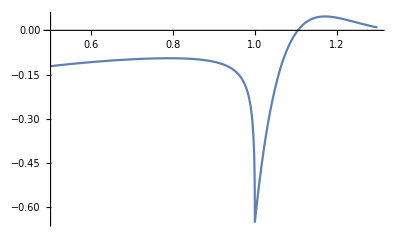

```mathematica
Plot[Evans[λ,sys4/.ϵ->0.1],{λ,0.5,1.3},PlotRange->All]
```

Zooming in we can see it remains continuous:

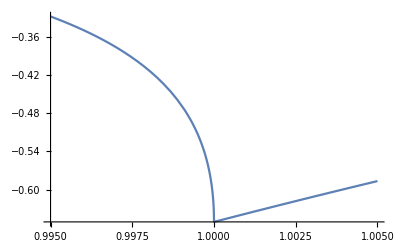

```mathematica
Plot[Evans[λ,sys4/.ϵ->0.1],{λ,0.995,1.005},PlotRange->All]
```

This occurs when the eigenvalues of the matrix A at x=π/2 become entirely imaginary. In general this happens when eigenvalues at either endpoint change type. However, the function is still continuous here.
Note that ToMatrixSystem relabels the eigenvalue to λ, which is [\FormalLambda] not λ.

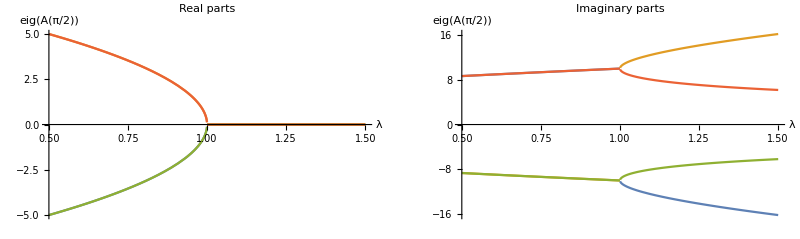

```mathematica
GraphicsRow[{Plot[Evaluate[Re@Eigenvalues[sys4[[1]]/.ϵ->1/10/.x->π/2]],{λ,0.5,1.5},PlotLabel->"Real parts", AxesLabel->{"λ","eig(A(π/2))"}],Plot[Evaluate[Im@Eigenvalues[sys4[[1]]/.ϵ->1/10/.x->π/2]],{λ,0.5,1.5},PlotLabel->"Imaginary parts",AxesLabel->{"λ","eig(A(π/2))"}]},ImageSize->800]
```

This can be removed by using the option NormalizationConstants in the Evans function:

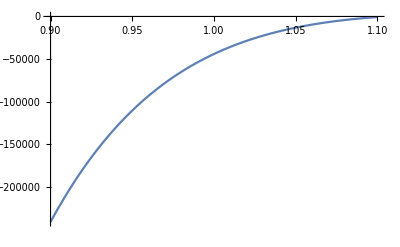

```mathematica
Plot[Evans[λ,sys4/.ϵ->0.1,NormalizationConstants->0],{λ,0.9,1.1}]
```

However, the values of the function are much larger for all values:

```mathematica
Evans[1,sys4/.ϵ->1/10,NormalizationConstants->0]
Evans[1,sys4/.ϵ->1/10]
```

-43957.3

-0.650472

FindRoot will converge to the same roots without the normalization in this case, but it can sometimes cause an issue with precision. It does need to be turned off in cases where one boundary condition is at a singular point of the differential equation (e.g. radial coordinates).

```mathematica
FindRoot[Evans[λ,sys4/.ϵ->1/10,NormalizationConstants->0],{λ,1.1}]
FindRoot[Evans[λ,sys4/.ϵ->1/10,NormalizationConstants->0],{λ,1.3}]
FindRoot[Evans[λ,sys4/.ϵ->1/10,NormalizationConstants->0],{λ,1.61}]
FindRoot[Evans[λ,sys4/.ϵ->1/10,NormalizationConstants->0],{λ,1.9}]
```

{λ→1.10517}

{λ→1.34269}

{λ→1.62184}

{λ→1.94586}

Example 5: Tenth order equation with constant coefficients

An example of a 10x10 matrix equation, subject to symmetric boundary conditions at x=0,1.

```mathematica
A2={{0,1,0,0,0,0,5,0,-5,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{-625 ω,-125/2,2,0,0,3,-300,0,300,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,-1.5,0.5,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,-169,0,0,0,0,9175+694 ω,0,811,0},{0,0,0,0,0,0,0,0,0,1},{0,672,0,0,0,0,3222,0,-709+694 ω,0}};
```

```mathematica
A2//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 5 | 0 | -5 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-625 ω | -125/2 | 2 | 0 | 0 | 3 | -300 | 0 | 300 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1.5 | 0.5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | -169 | 0 | 0 | 0 | 0 | 9175+694 ω | 0 | 811 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 672 | 0 | 0 | 0 | 0 | 3222 | 0 | -709+694 ω | 0)

Manually build the system here:

```mathematica
sys5={A2,DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],{x,0,1}};
```

Takes a few seconds  for the first evaluation while it builds up the 10 x10 matrix, faster  for the subsequent ones.

```mathematica
Evans[{ω,1},sys5]//AbsoluteTiming
```

{0.452783,-0.672945}

Each point takes longer to evaluate to evaluate for a large system like this, so ListPlot works better than Plot.

```mathematica
Evans[{ω,1},sys5]//AbsoluteTiming
```

{0.461368,-0.672945}

We can see there are a number of positive real eigenvalues:

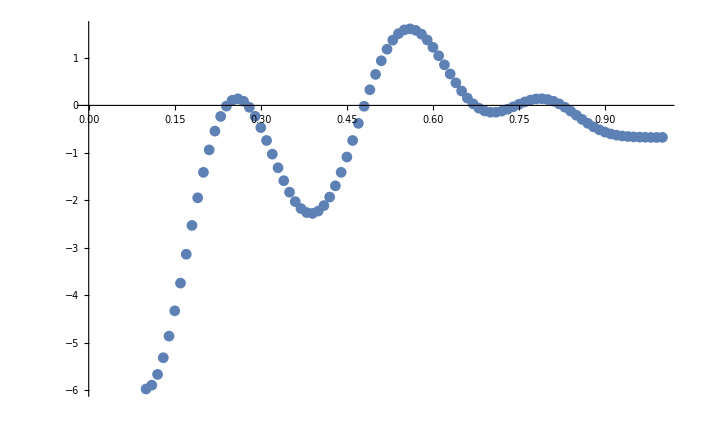

```mathematica
ListPlot[Table[{ωω,Evans[{ω,ωω},sys5]},{ωω,0.1,1,0.01}]]
```

```mathematica
FindRoot[Evans[{ω,ωω},sys5],{ωω,0.3}]
FindRoot[Evans[{ω,ωω},sys5],{ωω,0.5}]
FindRoot[Evans[{ω,ωω},sys5],{ωω,0.7}]
FindRoot[Evans[{ω,ωω},sys5],{ωω,0.72}]
FindRoot[Evans[{ω,ωω},sys5],{ωω,0.8}]
```

{ωω→0.277395}

{ωω→0.480499}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{ωω→0.24095}

{ωω→0.745487}

{ωω→0.824797}

Example 6: Fourth order equation with non-constant coefficients and infinite endpoints

An example with an infinite domain requiring the function w to decay at both ends. 
The equation is (d^4 w)/dx^4-(d^2 w)/dx^2+2(d^2(w w_0))/dx^2+λ w =0, where w_0(x)=3/2 sech^2(x/2), with w decaying at both positive and negative infinity.

To ensure that the function to decay at both ends, we can find the eigenvectors of the limiting matrix A as x approaches infinity. At negative (positive) infinity, the function must approach those eigenvectors corresponding to  positive (negative) eigenvalues of the function at these ends.
This is incorporated into Evans, which will assume that any missing boundary conditions should be of this form. Here we will make the system dependent on the value of the domain size L.

```mathematica
sys6[L_]=ToMatrixSystem[w''''[x]-w''[x]+2D[w0[x]w[x],{x,2}]+λ w[x]==0,{},w,{x,-L,L},λ]/.w0->Function[{x},3/2 Sech[x/2]^2]
```

{{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-λ-2 (-3/4 Sech[x/2]^4+3/2 Sech[x/2]^2 Tanh[x/2]^2),6 Sech[x/2]^2 Tanh[x/2],1-3 Sech[x/2]^2,0}},{},{},{x,-L,L}}

So we can set up a function that evaluates for a given λ_0 and domain length L_0:

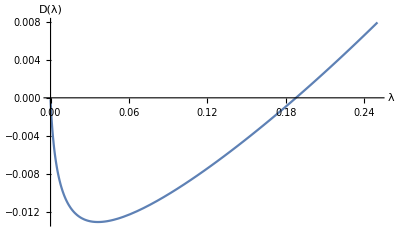

```mathematica
Plot[Evans[λ,sys6[10]],{λ,0,0.25},AxesLabel->{"λ","D(λ)"}]
```

As we varying the position at which the end point “infinity” conditions are applied at, the Evans function converges to the known root (λ_0=3/8):

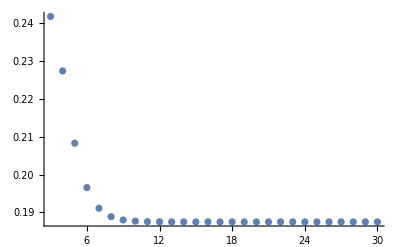

```mathematica
ListPlot[Table[{L,λ}/.FindRoot[Evans[λ,sys6[L]],{λ,0.2}],{L,3,30}],PlotRange->All]//Quiet
```

Alternatively, we can solve the same system but use the fact that everything is an even function to split at zero (so w'(0)=w'''(0)=0).

```mathematica
sys6b[L_]=ToMatrixSystem[w''''[x]-w''[x]+2D[w0[x]w[x],{x,2}]+λ w[x]==0,{w'[0]==0,w'''[0]==0},w,{x,0,L},λ]/.w0->Function[{x},3/2 Sech[x/2]^2];
```

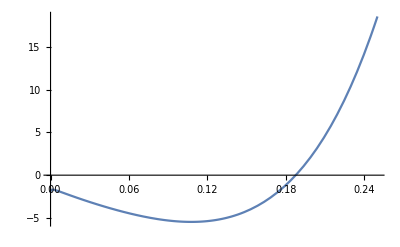

```mathematica
Plot[Evans[λ,sys6b[20]],{λ,0,0.25}]
```

Position of the roots are identical for the two methods of solution:

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

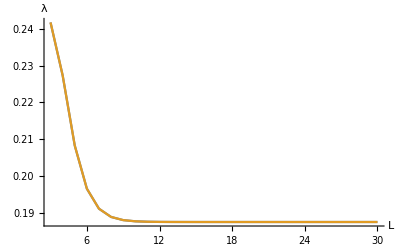

```mathematica
rootposa=Table[{L,λ}/.FindRoot[Evans[λ,sys6[L]],{λ,0.2}],{L,3,30}];
rootposb=Table[{L,λ}/.FindRoot[Evans[λ,sys6b[L]],{λ,0.2}],{L,3,30}];
ListLinePlot[{rootposa,rootposb},PlotRange->All,AxesLabel->{"L","λ"}]
```

Even if the two functions give different outputs, their roots (and hence their eigenvalues) coincide  (note the first function is multiplied by 20 to make the scales comparable).

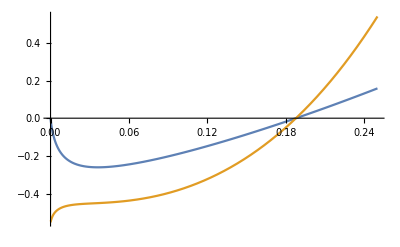

```mathematica
Plot[{20Evans[λ,sys6[10]],Evans[λ,sys6b[10]]},{λ,0,0.25}]
```

Example 7: Sixth order system, constructing neutral curves as parameters vary

Linear stability equations for cylinder rotating inside another, [ϵ^2 ∂_yy - 1]^2u(y) = ϵ^2 T V(y) v(y),  [ϵ^2 ∂_yy -1] v(y) = ϵ^2 T u(y) V' (y), ϵ u'(y) + I w(y) =0, where V(y) = 1-y.

Set up the equations, note that the equation for w does not contain any derivatives but the code handles that appropriately.

```mathematica
dd=(ϵ^2 D[#,{y,2}]-#)&;
sys7=ToMatrixSystem[{dd[dd[u[y]]]==ϵ^2 T V[y]v[y],dd[v[y]]==ϵ^2 u[y]V'[y],ϵ u'[y]+ I w[y]==0},{u[0]==0,v[0]==0,w[0]==0,u[1]==0,v[1]==0,w[1]==0},{u,v,w},{y,0,1},T];
```

Define a function to calculate the Evans function for a given ϵ and T:

```mathematica
Clear[tempfn];
tempfn[ee_?NumericQ,T_?NumericQ]:=Evans[T,sys7/.V->Function[{y},1-y]/.ϵ->ee]
```

Find a value of T for ϵ = 0.1:

```mathematica
FindRoot[tempfn[1/10,t],{t,20000}]
```

{t→26242.5}

Loop through varying ϵ to construct sections of a neutral curve. Start at the previous value to stay along the same curve (takes a while to follow the roots)

```mathematica
lastroot={T->26242};
etab=Monitor[Table[lastroot=FindRoot[tempfn[e,T],{T,T/.lastroot},DampingFactor->0.2];{e,T}/.lastroot,{e,0.1,1,0.1}],e];//Quiet
```

```mathematica
lastroot={T->26242};
etab2=Monitor[Table[lastroot=FindRoot[tempfn[e,T],{T,1.4*T/.lastroot},DampingFactor->0.2];{e,T}/.lastroot,{e,Reverse@Range[0.03,0.1,0.005]}],e];//Quiet
```

Plot the neutral curve:

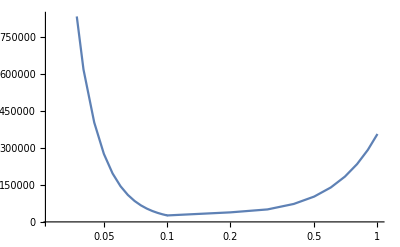

```mathematica
ListLogLinearPlot[Sort@(Join@@{etab,etab2}),Joined->True]
```

There is another neutral curve at higher values of T:

```mathematica
lastroot={T->226242};
etab3=Monitor[Table[lastroot=FindRoot[tempfn[e,T],{T,T/.lastroot},DampingFactor->0.2];{e,T}/.lastroot,{e,0.1,1,0.1}],e];
```

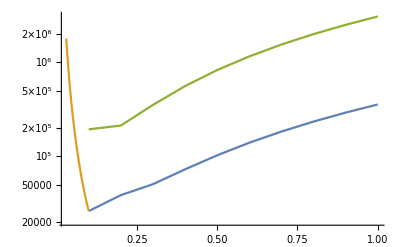

```mathematica
ListLogPlot[{etab,etab2,etab3},Joined->True,PlotRange->All]
```

These additional roots for a given value of T can seen when plotting at a fixed value of ϵ:

NDSolve::ndsz: At y == 3.00927×10^-36, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At y == 4.81482×10^-35, step size is effectively zero; singularity or stiff system suspected.

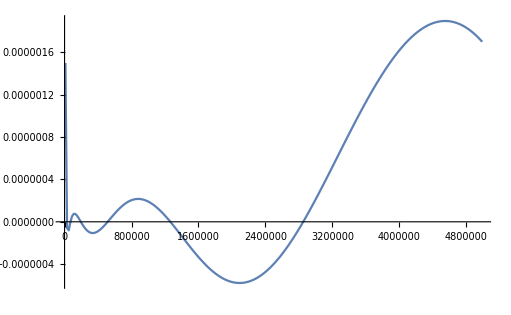

```mathematica
Table[{T,tempfn[0.1,T]},{T,10^4,5*10^6,2*10^4}]//ListLinePlot
```

Example 8: Second order system with interface

The method also works very well for systems with two domains connected by an interface, as the matching point can be placed there.

Define some equations and endpoints:

```mathematica
x1=-2;x2=0;x3=5;
eq1=y''[x]-2y'[x]+σ^2 y[x]==0;
eq2=z''[x]-(5+1/5)z'[x]-σ^2 z[x]==0;
matchconds={y[x2]==z[x2],y'[x2]+y[x2]==-2z'[x2]+z[x2]};
bcs1={y'[x1]==0};
bcs2={z[x3]==0};
```

We can solve this explicitly:

```mathematica
ysub=DSolve[eq1,y,x][[1]];
zsub=DSolve[eq2,z,x,GeneratedParameters->(C[#+2]&)][[1]];
det=Transpose[Table[Coefficient[Join[bcs1,bcs2,matchconds]/.ysub/.zsub/.Equal->Subtract,ii],{ii,Array[C,4]}]]//Det//Simplify;
```

NSolve is not very good at finding roots for this system, and the symbolic solution includes spurious solutions at values where the ODE has a repeated root, e.g. σ= ±1, ±2.6 ⅈ.

```mathematica
nsol=NSolve[{det==0,0.1<Abs[σ]<10},σ]
```

{{σ→-5.85664+0. ⅈ},{σ→-1.+0. ⅈ},{σ→0.-2.6 ⅈ},{σ→0.+2.6 ⅈ},{σ→0.-2.68176 ⅈ},{σ→0.+2.68176 ⅈ},{σ→0.-2.91216 ⅈ},{σ→0.+2.91216 ⅈ},{σ→0.-3.25753 ⅈ},{σ→0.+3.25753 ⅈ},{σ→1.+0. ⅈ},{σ→5.85664+0. ⅈ}}

FindRoot is better:

```mathematica
roots=Table[FindRoot[det==0,{σ,ii}],{ii,{1.6,3,4.4}}]//Quiet//Chop
```

{{σ→1.61479},{σ→2.88141},{σ→4.33898}}

LinearMatrixForm with some additional arguments can process these equations:

```mathematica
sys8=ToMatrixSystem[{eq1,eq2},{bcs1,bcs2,matchconds},{y,z},{x,x1,x2,x3},σ];
```

And then Evans will evaluate for a value of the eigenvalue, with roots at the same points as found via the determinant method.

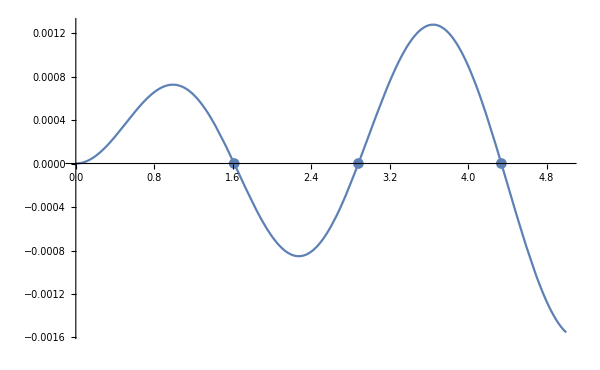

```mathematica
Show[Plot[Evans[σ,sys8],{σ,0,5}],ListPlot[{σ,0}/.roots],ImageSize->600]
```

Example 9: Fourth order system with an interface, constant coefficients

Set up some arbitrary equations to be solved in the two regimes, for eigenvalue σ,
y''''(x)+5 y''(x)+σ^4 y(x)==0       in x_1≤x≤x_2
z''''(x)-σ^4 z(x)==0                               in x_2≤x≤x_3
subject to
y'(x_1)=0, y''(x_1)=0, z'(x_3)=0, z'''(x_3)=0
with interface conditions
y(x_2)=z(x_2),      y'(x_2)+y'''(x_2)=-2z'(x_2)+z(x_2)-z'''(x_2),    3 y''(x_2)=0.2 z(x_2)+2z''(x_2)-5z'''(x_2),   -3 y'''(x_2)=z'(x_2)-z'''(x_2)

```mathematica
x1=-5;x2=1;x3=2;
eq1=y''''[x]+5 y''[x]+σ^4 y[x]==0;
eq2=z''''[x]-σ^4 z[x]==0;
matchconds={y[x2]==z[x2],y'[x2]+y'''[x2]==-2z'[x2]+z[x2]-z'''[x2],3y''[x2]==0.2z[x2]+2z''[x2]-5z'''[x2],-3y'''[x2]==z'[x2]-z'''[x2]};
bcs1={y'[x1]==0,y''[x1]==0};
bcs2={z'[x3]==0,z'''[x3]==0};
```

These equations are simple enough to be solved exactly in the two regions:

```mathematica
ysub=DSolve[eq1,y,x][[1]]
zsub=DSolve[eq2,z,x,GeneratedParameters->(C[#+4]&)][[1]]
```

{y→Function[{x},ⅇ^((x √(-5-√(25-4 σ^4)))/(√2)) C[1]+ⅇ^(-(x √(-5-√(25-4 σ^4)))/(√2)) C[2]+ⅇ^((x √(-5+√(25-4 σ^4)))/(√2)) C[3]+ⅇ^(-(x √(-5+√(25-4 σ^4)))/(√2)) C[4]]}

{z→Function[{x},ⅇ^(-x σ) C[6]+ⅇ^(x σ) C[8]+C[5] Cos[x σ]+C[7] Sin[x σ]]}

Substituting these solutions into the boundary and matching conditions, we can find a coefficient matrix for the constants C[i]:

```mathematica
(coefmat=Transpose[Table[Coefficient[Join[bcs1,bcs2,matchconds]/.ysub/.zsub/.Equal->Subtract,ii],{ii,Array[C,4+4]}]])//MatrixForm
```

((ⅇ^(-(5 √(-5-√(25-4 σ^4)))/(√2)) √(-5-√(25-4 σ^4)))/(√2) | -(ⅇ^((5 √(-5-√(25-4 σ^4)))/(√2)) √(-5-√(25-4 σ^4)))/(√2) | (ⅇ^(-(5 √(-5+√(25-4 σ^4)))/(√2)) √(-5+√(25-4 σ^4)))/(√2) | -(ⅇ^((5 √(-5+√(25-4 σ^4)))/(√2)) √(-5+√(25-4 σ^4)))/(√2) | 0 | 0 | 0 | 0
1/2 ⅇ^(-(5 √(-5-√(25-4 σ^4)))/(√2)) (-5-√(25-4 σ^4)) | 1/2 ⅇ^((5 √(-5-√(25-4 σ^4)))/(√2)) (-5-√(25-4 σ^4)) | 1/2 ⅇ^(-(5 √(-5+√(25-4 σ^4)))/(√2)) (-5+√(25-4 σ^4)) | 1/2 ⅇ^((5 √(-5+√(25-4 σ^4)))/(√2)) (-5+√(25-4 σ^4)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -σ Sin[2 σ] | -ⅇ^(-2 σ) σ | σ Cos[2 σ] | ⅇ^(2 σ) σ
0 | 0 | 0 | 0 | σ^3 Sin[2 σ] | -ⅇ^(-2 σ) σ^3 | -σ^3 Cos[2 σ] | ⅇ^(2 σ) σ^3
ⅇ^((√(-5-√(25-4 σ^4)))/(√2)) | ⅇ^(-(√(-5-√(25-4 σ^4)))/(√2)) | ⅇ^((√(-5+√(25-4 σ^4)))/(√2)) | ⅇ^(-(√(-5+√(25-4 σ^4)))/(√2)) | -Cos[σ] | -ⅇ^-σ | -Sin[σ] | -ⅇ^σ
(ⅇ^((√(-5-√(25-4 σ^4)))/(√2)) √(-5-√(25-4 σ^4)))/(√2)+(ⅇ^((√(-5-√(25-4 σ^4)))/(√2)) (-5-√(25-4 σ^4))^(3/2))/(2 √2) | -(ⅇ^(-(√(-5-√(25-4 σ^4)))/(√2)) √(-5-√(25-4 σ^4)))/(√2)-(ⅇ^(-(√(-5-√(25-4 σ^4)))/(√2)) (-5-√(25-4 σ^4))^(3/2))/(2 √2) | (ⅇ^((√(-5+√(25-4 σ^4)))/(√2)) √(-5+√(25-4 σ^4)))/(√2)+(ⅇ^((√(-5+√(25-4 σ^4)))/(√2)) (-5+√(25-4 σ^4))^(3/2))/(2 √2) | -(ⅇ^(-(√(-5+√(25-4 σ^4)))/(√2)) √(-5+√(25-4 σ^4)))/(√2)-(ⅇ^(-(√(-5+√(25-4 σ^4)))/(√2)) (-5+√(25-4 σ^4))^(3/2))/(2 √2) | -Cos[σ]-2 σ Sin[σ]+σ^3 Sin[σ] | -ⅇ^-σ-2 ⅇ^-σ σ-ⅇ^-σ σ^3 | 2 σ Cos[σ]-σ^3 Cos[σ]-Sin[σ] | -ⅇ^σ+2 ⅇ^σ σ+ⅇ^σ σ^3
-15/2 ⅇ^((√(-5-√(25-4 σ^4)))/(√2))-3/2 ⅇ^((√(-5-√(25-4 σ^4)))/(√2)) √(25-4 σ^4) | -15/2 ⅇ^(-(√(-5-√(25-4 σ^4)))/(√2))-3/2 ⅇ^(-(√(-5-√(25-4 σ^4)))/(√2)) √(25-4 σ^4) | -15/2 ⅇ^((√(-5+√(25-4 σ^4)))/(√2))+3/2 ⅇ^((√(-5+√(25-4 σ^4)))/(√2)) √(25-4 σ^4) | -15/2 ⅇ^(-(√(-5+√(25-4 σ^4)))/(√2))+3/2 ⅇ^(-(√(-5+√(25-4 σ^4)))/(√2)) √(25-4 σ^4) | -0.2 Cos[σ]+2 σ^2 Cos[σ]+5 σ^3 Sin[σ] | -0.2 ⅇ^-σ-2 ⅇ^-σ σ^2-5 ⅇ^-σ σ^3 | -5 σ^3 Cos[σ]-0.2 Sin[σ]+2 σ^2 Sin[σ] | -0.2 ⅇ^σ-2 ⅇ^σ σ^2+5 ⅇ^σ σ^3
(15 ⅇ^((√(-5-√(25-4 σ^4)))/(√2)) √(-5-√(25-4 σ^4)))/(2 √2)+(3 ⅇ^((√(-5-√(25-4 σ^4)))/(√2)) √(25-4 σ^4) √(-5-√(25-4 σ^4)))/(2 √2) | -(15 ⅇ^(-(√(-5-√(25-4 σ^4)))/(√2)) √(-5-√(25-4 σ^4)))/(2 √2)-(3 ⅇ^(-(√(-5-√(25-4 σ^4)))/(√2)) √(25-4 σ^4) √(-5-√(25-4 σ^4)))/(2 √2) | (15 ⅇ^((√(-5+√(25-4 σ^4)))/(√2)) √(-5+√(25-4 σ^4)))/(2 √2)-(3 ⅇ^((√(-5+√(25-4 σ^4)))/(√2)) √(25-4 σ^4) √(-5+√(25-4 σ^4)))/(2 √2) | -(15 ⅇ^(-(√(-5+√(25-4 σ^4)))/(√2)) √(-5+√(25-4 σ^4)))/(2 √2)+(3 ⅇ^(-(√(-5+√(25-4 σ^4)))/(√2)) √(25-4 σ^4) √(-5+√(25-4 σ^4)))/(2 √2) | σ Sin[σ]+σ^3 Sin[σ] | ⅇ^-σ σ-ⅇ^-σ σ^3 | -σ Cos[σ]-σ^3 Cos[σ] | -ⅇ^σ σ+ⅇ^σ σ^3)

We can find zeroes of the determinant of this matrix using FindRoot:

```mathematica
detRoots={σ,0}/.(FindRoot[Det[coefmat],{σ,#}]&/@{1.3,1.5,2,4})//Chop//Quiet;
```

This determinant method struggles for more complicated systems.
Instead we can use the function ToMatrixSystem to convert this system into the appropriate form for the compound matrix method:

```mathematica
sys9=ToMatrixSystem[{eq1,eq2},{bcs1,bcs2,matchconds},{y,z},{x,x1,x2,x3},σ];
```

Now given a test value of σ, we can find the Evans function there:

```mathematica
Evans[1,sys9]
```

-11.0729

And then plot the Evans function as we change the value of σ, and we find the same values as the determinant method:

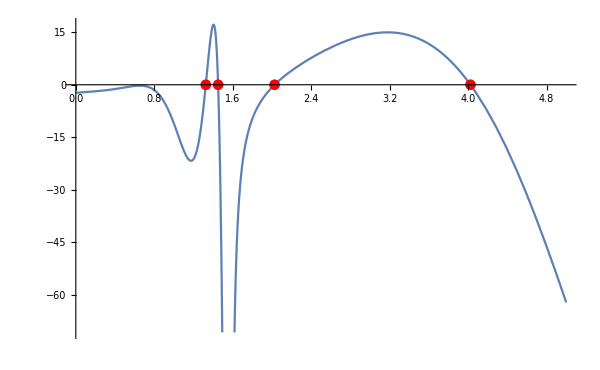

```mathematica
Show[Plot[Evans[{σ,ss},sys9],{ss,0,5}],ListPlot[detRoots,PlotStyle->Red],ImageSize->600]
```

Example 10: Interface with non-constant coefficients

This example is part of the paper “Curvature delays growth-induced wrinkling” published in Physical Review E by Jia, Pearce and Goriely: (https://link.aps.org/doi/10.1103/PhysRevE.98.033003). Here a thin growing surface is attached to an elastic cylinder.

So we define our governing equation and boundary conditions:

```mathematica
goveqn=((-1+n^2) U[r] (3-4 λ α^2+n^2 α^4)+r ((3+n^2-2 (2+n^2) λ α^2-3 n^2 α^4+2 n^2 λ α^6) U'[r]+r (-(3+n^2-8 λ α^2+n^2 α^4) U''[r]+r ((2+4 λ α^2) Derivative[3][U][r]+r Derivative[4][U][r]))))/r^4;
Be11=((-1+n^2) U[r] (-1+2 λ α^2)+r (-(1+2 n^2-2 λ α^2+n^2 α^4) U'[r]+r (2 (1+λ α^2) U''[r]+r Derivative[3][U][r])))/r^3;
Be21=((-1+n^2) U[r]+r (U'[r]+r U''[r]))/r^2;
fsubs={U->Uf,λ->λf,α->αf,μ->μf};
ssubs={U->Us,λ->λs,α->αs,μ-> μs};
sub1={g1f->g,g2f->g,g1s->1,g2s->1,λf->1,λs->1,μf->ξ μs,A->1,B->1+η,αs->1/(√λs),αf->rf/(√(λf(rf^2-c1f))),c1f->(Js-Jf)A^2,Js->g1s g2s,Jf->g1f g2f,ra->√(Js A^2),rb->√(Jf B^2+c1f)};
inteqn={U[r],U'[r],1/μs μ/α^2 Be11,1/μs μ/α^2 Be21};
inteqn2=Thread[(inteqn/.fsubs)==(inteqn/.ssubs)]//.sub1/.rf->ra//.sub1;
leftBCs={U[r]==0,U'[r]==0}/.ssubs/.r->rϵ;
rightBCs={Be11==0,Be21==0}/.fsubs/.r->rb//.sub1/.rf->rb//.sub1;
sys10=ToMatrixSystem[{(goveqn==0)/.fsubs//.sub1/.rf->r,(goveqn==0)/.ssubs//.sub1/.rf->r},Flatten[{leftBCs,rightBCs,inteqn2/.rf->r/.r->ra}]//.sub1,{Us,Uf},{r,rϵ,ra,rb}//.sub1,g];
```

Now for a given set of constants we can evaluate the Evans function at a fixed value of g (the eigenvalue):

```mathematica
Evans[1,sys10/.{n->5,η->0.1,ξ->2,rϵ->0.001},NormalizationConstants->0]
```

8.38583×10^29

Note that as there is a coordinate induced singularity at r=0, so the normalization constants need to be removed. This means the values of the Evans function are much larger.

```mathematica
Plot[Evans[g,sys10/.{n->5,η->0.1,ξ->2,rϵ->0.001},NormalizationConstants->0],{g,1,1.6}]
```

-Graphics-

In this problem, the wave number n is determined by the value which has the minimal eigenvalue of g. For these constants, the wave number is given 8 here:

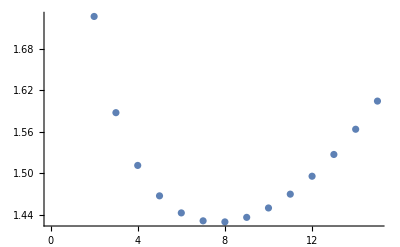

```mathematica
ListPlot[Table[{n,g}/.FindRoot[Evans[g,sys10/.{η->0.1,ξ->2,rϵ->0.001},NormalizationConstants->0],{g,1.5}],{n,2,15}]]//Quiet
```

These calculated minimal wave numbers match very closely with analytical results (see the paper) as the constants are changed, verifying that the code is working well for these interface problems.

Example 11: Fourth order, eigenvalue in the integration range

This example comes from https://mathematica.stackexchange.com/questions/166952/. Here the eigenvalue is the length of the domain, and also appears in the equation.

```mathematica
ode=w''''[x]+(L-x) w''[x]-w'[x]== 0;
BCs={w[0]==0,w'[0]==0,w''[L]== 0,w'''[L]==0};
```

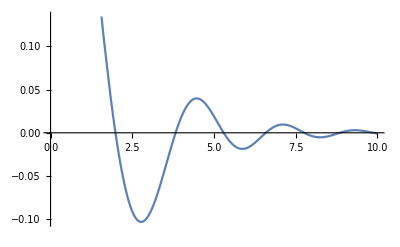

```mathematica
sys11=ToMatrixSystem[ode,BCs,w,{x,0,L},L];
Plot[Evans[L,sys11],{L,0,10}]
```

The first root is given by:

```mathematica
FindRoot[Evans[L,sys11],{L,2.5}]
```

{L0→1.98635}

Example 12: Petterson - Konig’s Rod

Petterson-Konig’s Rod is a singular eigenvalue problem coming from elasticity, where the eigenvalue also occurs in the boundary conditions. 
It is given by: y''''(x) = λ y''(x), y(0)=0, y'(0)=0, y''(1)=0, y'''(1) - λ (1-γ) y'(1)=0 , where γ  is a parameter.
The general solution is given by:

```mathematica
DSolveValue[y''''[x]==λ y''[x],y[x],x]//Simplify
```

(ⅇ^(x √λ) C[1]+ⅇ^(-x √λ) C[2])/λ+C[3]+x C[4]

The eigenvalues can be found as cos(√λ)=γ/(γ-1). As γ approaches 0.5, the eigenvalues become complex.

Setup the system:

```mathematica
sys12=ToMatrixSystem[y''''[x]==λ y''[x],{y[0]==0,y'[0]==0,y''[1]==0,y'''[1]-λ(1-γ)y'[1]==0},y,{x,0,1},λ];
```

```mathematica
FindRoot[Evans[λ,sys12/.γ->0.1],{λ,-3},AccuracyGoal->8,PrecisionGoal->10]
```

{λ→-2.82959}

So as we increase the value of γ, the eigenvalues coalesce, which can be seen easily in the Evans function.

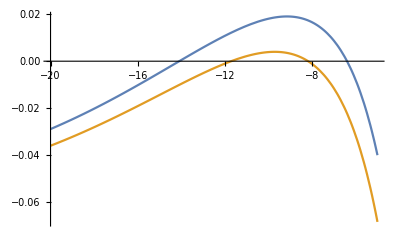

```mathematica
Plot[{Evans[λ,sys12/.γ->0.45],Evans[λ,sys12/.γ->0.49]},{λ,-20,-5}]
```

If we increase the WorkingPrecision, we can get closer to the point at which the eigenvalues go complex:

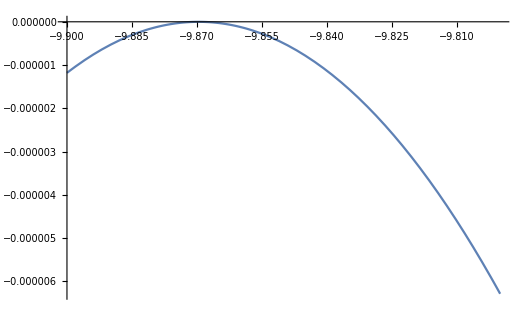

```mathematica
Plot[Evans[λ,sys12/.γ->1/2,WorkingPrecision->30],{λ,-99/10,-98/10},WorkingPrecision->30]//Quiet
```

```mathematica
FindRoot[Evans[λ,sys12/.γ->5/10],{λ,-10+I},AccuracyGoal->8,PrecisionGoal->10]
```

{λ→-9.86959+0.00879487 ⅈ}

```mathematica
FindRoot[Evans[λ,sys12/.γ->5/10,WorkingPrecision->28],{λ,-8+I},AccuracyGoal->8,PrecisionGoal->10,WorkingPrecision->30]
```

{λ→-9.86960429236614538762705174376+0.000928659273917282181800584345923 ⅈ}